```mathematica
ep=0.08;β=0.8;γ=0.5;
τ=131.56;α=0.081;γt=1.6221;
xmin=-50;xmax=50;maxtime=100; dd1=2;dd2=0.001;δ=7.5;
eqn=FindRoot[v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
d2=2;d1=0.5;LL=2;
(*ρ[x_]=d2*d1^(3/2)/(d1+x^2)^(3/2);(*no block*)*)
ρ[x_]=Which[Abs[x]<=LL,d2,True,0];
eqn1=FindRoot[v-v^3/3-(v+β)/γ,{v,-1}];
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

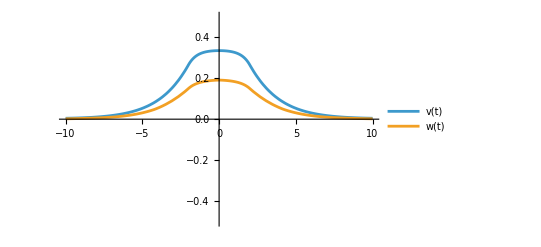

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

-Graphics3D-

```mathematica
(*Step 1: Starting from the equilibrium, lead to an ok initial guess*)
{V1,W1}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-u[t,x])(u[t,x]-α)+(1+α-3u[t,x])ρ[x]^2/2- w[t,x], τ D[w[t, x], t] == u[t, x] - γt w[t, x], 
u[0, x] ==0, 
u[t, xmin] == 0, 
u[t, xmax] == 0, w[0, x] ==0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
{V2,W2}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-u[t,x])(u[t,x]-α)+(1+α-3u[t,x])ρ[x]^2/2- w[t,x], τ D[w[t, x], t] == u[t, x] - γt w[t, x], 
u[0, x] ==V1[maxtime,x], 
u[t, xmin] == 0, 
u[t, xmax] == 0, w[0, x] ==W1[maxtime,x]}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot[{V2[maxtime,x],W2[maxtime,x]},{x,-10,10},PlotRange->{-0.5,0.5},PlotLegends->{"v(t)","w(t)"}]
(*Step 3: First approximation to autonomus solution, uses previous iteration*)
{V3,W3}=
NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-u[t,x])(u[t,x]-α)+(1+α-3u[t,x])ρ[x]^2/2- w[t,x], τ D[w[t, x], t] == u[t, x] - γt w[t, x], 
u[0, x] ==V2[maxtime,x]+Which[Abs[x-6] <=2, 0.85, True, 0],
u[t, xmin] == 0, 
u[t, xmax] == 0, w[0, x] ==W2[maxtime,x]}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot3D[{V3[t,x]}, {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
```

```mathematica
Animate[Plot[{V3[t,x]-V2[maxtime,x],W3[t,x]-W2[maxtime,x]},{x,xmin,xmax},PlotRange->{-1,2}],{t,0,maxtime},AnimationRunning->False,AnimationRepetitions->1]
```

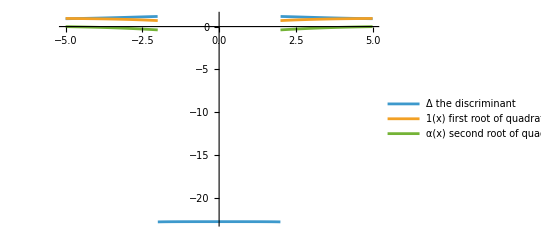

```mathematica
(*P1 and P2 are the root in the factorization after the change of variables*)
g[x_]=(1+α-3V2[maxtime,x])^2-4(α+3V2[maxtime,x]^2-2(1+α )V2[maxtime,x]+3ρ[x]^2/2);
p1[x_]=0.5(1+α-3V2[maxtime,x])+0.5Sqrt[(1+α-3V2[maxtime,x])^2-4(α+3V2[maxtime,x]^2-2(1+α )V2[maxtime,x]+3ρ[x]^2/2)];
p2[x_]=0.5(1+α-3V2[maxtime,x])-0.5Sqrt[(1+α-3V2[maxtime,x])^2-4(α+3V2[maxtime,x]^2-2(1+α )V2[maxtime,x]+3ρ[x]^2/2)];
Plot[{g[x],p1[x],p2[x]},{x,-5,5},PlotRange->All,PlotLegends->{"Δ the discriminant","1(x) first root of quadratic ","α(x) second root of quadratic"}]
```

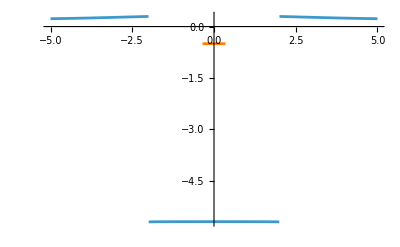

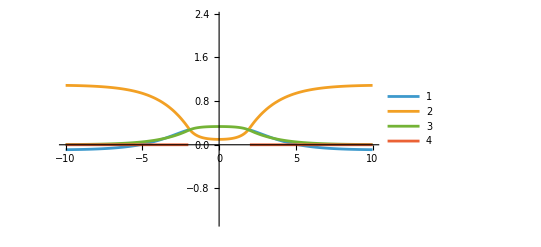

```mathematica
(*Maximum of the quadratic polynomial with coefficientes P1 and P2*)
a1[x_]=-α+2V2[maxtime,x](1+α)-3V2[maxtime,x]^2-3ρ[x]^2/2;
a2[x_]=1+α-3V2[maxtime,x];
(*the maximum of a quadratic is (4ac-b^2)/(4a) *)
g1=Plot[(4a1[x]+a2[x]^2)/4,{x,-5,5},PlotRange->All];
g2=Plot[-0.5,{x,-0.35,0.35},PlotStyle->Orange];
Show[g1,g2]
Plot[{a1[x],a2[x],V2[maxtime,x],ρ[x]^2},{x,-10,10},PlotLegends->Automatic]
```

```mathematica
(*Search For homoclinic of (0,0)*)
simulationTime=1;
{V5}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](a1[x]-a2[x]u[t,x]-u[t,x]^2)+u[t,x]/γt,
u[0, x] ==Which[x<0,1,True,0], 
u[t, xmin] == 1, 
u[t, xmax] == 0}, {u}, {t, 0, simulationTime}, {x, xmin, xmax}];
Animate[Plot[{V5[t,x]},{x,xmin,xmax},PlotRange->{-1,2}],{t,0,simulationTime},AnimationRunning->False,AnimationRepetitions->1]
Animate[Plot[{ u(a1[x]-a2[x]u-u^2)+u/γt},{u,0,1.5},PlotRange->{-1,2}],{x,-10,10},AnimationRunning->False,AnimationRepetitions->1]
```

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

0.3

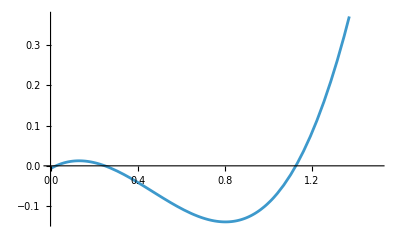

```mathematica
α=0.4;γt=10;
ρ1=0.1;
α-1/γt
Plot[-(1+α)ρ1^2/2+(3ρ1^2/2+α-1/γt)v-(1+α)v^2+v^3,{v,0,1.5}]
```

-1.5

1

0.05

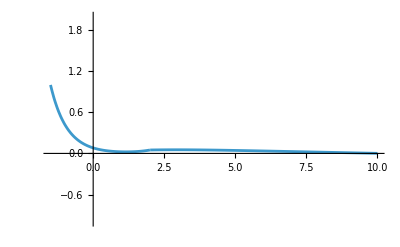

```mathematica
startPoint=-LL+0.5
valuestartPoint=1
valueLL=0.05

{V6a}=NDSolveValue[{0==dd1 D[u[ x], x, x] + u[x](a1[x]-a2[x]u[x]-u[x]^2)+u[x]/γt,
u[startPoint] ==valuestartPoint, 
u[LL] ==valueLL}, {u}, {x,startPoint,LL},Method->{"PDEDiscretization"->"FiniteElement"}];
{V6b}=NDSolveValue[{0==dd1 D[u[ x], x, x] + u[x](a1[x]-a2[x]u[x]-u[x]^2)+u[x]/γt,
u[LL] ==valueLL, 
u[10] ==0.001}, {u}, {x,LL,10},Method->{"PDEDiscretization"->"FiniteElement"}];
Plot[{Which[x<LL,V6a[x],True,V6b[x]]},{x,startPoint,10},PlotRange->{-1,2}]
```